# Q - values in different quadrants

```mathematica
QvaluesADvsAD[t_, r_, p_, s_, epsilon_, d_]:={{-(2 p-epsilon p+epsilon t)/(2 (-1+d)),-1/(2 (-1+d))(2 d p-d epsilon p+epsilon r-d epsilon r+2 s-2 d s-epsilon s+d epsilon s+d epsilon t)},{-(2 p-epsilon p+epsilon t)/(2 (-1+d)), -1/(2 (-1+d))(2 d p-d epsilon p+epsilon r-d epsilon r+2 s-2 d s-epsilon s+d epsilon s+d epsilon t)}  }
```

```mathematica
QvaluesADvsAGT[t_, r_, p_, s_, epsilon_, d_]:={{-1/(2 (-1+d))(2 p-2 d p-epsilon p+2 d epsilon p+2 d t+epsilon t-2 d epsilon t), -1/(2 (-1+d))(2 d epsilon p-d^2 epsilon p-d epsilon^2 p+d^2 epsilon^2 p+epsilon r-d epsilon r+2 s-2 d s-epsilon s+d epsilon s+2 d t-2 d epsilon t+d^2 epsilon t+d epsilon^2 t-d^2 epsilon^2 t)}, {-(epsilon p+2 t-epsilon t)/(2 (-1+d)), -1/(2 (-1+d))(2 d p-2 d^2 p-2 d epsilon p+3 d^2 epsilon p+d epsilon^2 p-d^2 epsilon^2 p+2 r-2 d r-epsilon r+d epsilon r+epsilon s-d epsilon s+2 d^2 t+2 d epsilon t-3 d^2 epsilon t-d epsilon^2 t+d^2 epsilon^2 t)}}
```

```mathematica
QvaluesADvsAC[t_, r_, p_, s_, epsilon_, d_]:={{-(epsilon p+2 t-epsilon t)/(2 (-1+d)), -1/(2 (-1+d))(d epsilon p+2 r-2 d r-epsilon r+d epsilon r+epsilon s-d epsilon s+2 d t-d epsilon t)}, {-(epsilon p+2 t-epsilon t)/(2 (-1+d)), -1/(2 (-1+d))(d epsilon p+2 r-2 d r-epsilon r+d epsilon r+epsilon s-d epsilon s+2 d t-d epsilon t)}}
```

```mathematica
QvaluesGTvsGT[t_, r_, p_, s_, epsilon_, d_]:={{-1/(2 (-1+d))(2 d p+epsilon p-2 d epsilon p+2 t-2 d t-epsilon t+2 d epsilon t), -((2 d epsilon p-d epsilon^2 p+4 r-4 d r-2 epsilon r+2 d epsilon r+2 epsilon s-2 d epsilon s+d epsilon^2 t)/(2 (-1+d) (2-2 d+d epsilon)))},{-(2 p-epsilon p+epsilon t)/(2 (-1+d)), -((4 d p-4 d^2 p-4 d epsilon p+6 d^2 epsilon p+d epsilon^2 p-2 d^2 epsilon^2 p+2 epsilon r-2 d epsilon r+4 s-8 d s+4 d^2 s-2 epsilon s+6 d epsilon s-4 d^2 epsilon s+2 d epsilon t-2 d^2 epsilon t-d epsilon^2 t+2 d^2 epsilon^2 t)/(2 (-1+d) (2-2 d+d epsilon)))}}
```

BR (GT) -> GT, BR(AD)-> AD, BR(AGT)-> AD and BR(AC)-> AD

AD -> (+, +), GT -> (-, +), AGT - > (+, -), AC-> (-, -)

(AD, AD), (AD, GT), (AD, AGT), (AD, AC)
(GT, AD), (GT, GT), (GT, AGT), (GT, AC)
(AGT, AD), (AGT, GT), (AGT, AGT), (AGT, AC)
(AC, AD), (AC, GT), (AC, AGT), (AC, AC)

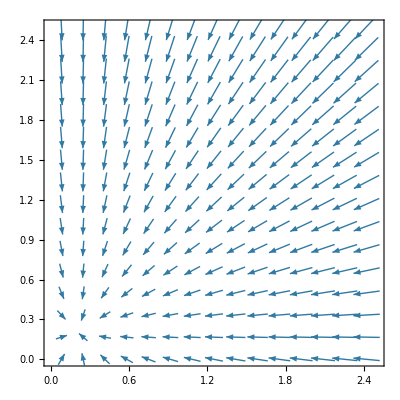
{-Graphics-,-Graphics-}

```mathematica
With[{t=1, s=0, r=0.7, p=0.2, epsilon=0.1, d=0.6, alpha=0.3},{VectorPlot[{ alpha (QvaluesADvsAD[t, r, p, s, epsilon, d][[1]][[1]]-QvaluesADvsAD[t, r, p, s, epsilon, d][[1]][[2]]-x), alpha (QvaluesADvsAD[t, r, p, s, epsilon, d][[1]][[1]]- QvaluesADvsAD[t, r, p, s, epsilon, d][[1]][[2]]-y)}, {x,0,1/(1-d)}, {y,0, 1/(1-d)}, Axes->True, VectorScale->{Medium,1/3,Automatic},VectorScaling->Automatic, VectorColorFunction->None]
,
VectorPlot[{ alpha (QvaluesADvsAD[t, r, p, s, epsilon, d][[2]][[1]]-QvaluesADvsAD[t, r, p, s, epsilon, d][[2]][[2]]-x), alpha (QvaluesADvsAD[t, r, p, s, epsilon, d][[2]][[1]]- QvaluesADvsAD[t, r, p, s, epsilon, d][[2]][[2]]-y)}, {x,0,1/(1-d)}, {y,0, 1/(1-d)}, Axes->True, VectorScale->{Medium,1/3,Automatic},VectorScaling->Automatic, VectorColorFunction->None]}]
```

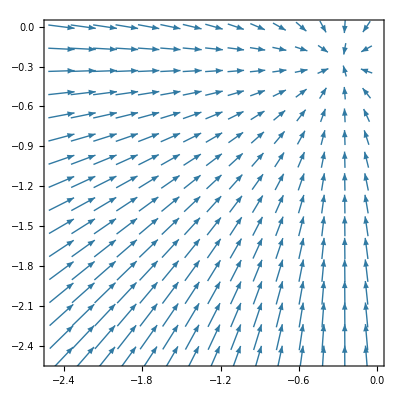
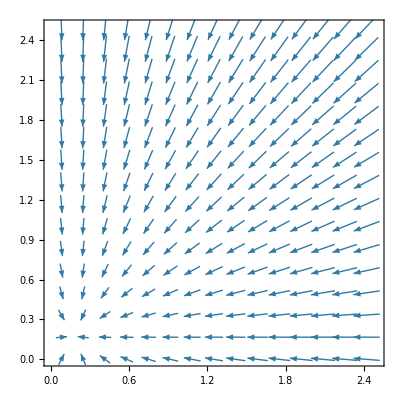

```mathematica
With[{t=1, s=0, r=0.7, p=0.2, epsilon=0.1, d=0.6, alpha=0.3},{VectorPlot[{ alpha (QvaluesGTvsGT[t, r, p, s, epsilon, d][[1]][[1]]-QvaluesGTvsGT[t, r, p, s, epsilon, d][[1]][[2]]-x), alpha (QvaluesGTvsGT[t, r, p, s, epsilon, d][[1]][[1]]- QvaluesGTvsGT[t, r, p, s, epsilon, d][[1]][[2]]-y)}, {x,-1/(1-d),0}, {y,- 1/(1-d), 0}, Axes->True, VectorScale->{Medium,1/3,Automatic},VectorScaling->Automatic, VectorColorFunction->None]
,
VectorPlot[{ alpha (QvaluesGTvsGT[t, r, p, s, epsilon, d][[2]][[1]]-QvaluesGTvsGT[t, r, p, s, epsilon, d][[2]][[2]]-x), alpha (QvaluesGTvsGT[t, r, p, s, epsilon, d][[2]][[1]]- QvaluesGTvsGT[t, r, p, s, epsilon, d][[2]][[2]]-y)}, {x,0,1/(1-d)}, {y,0, 1/(1-d)}, Axes->True, VectorScale->{Medium,1/3,Automatic},VectorScaling->Automatic, VectorColorFunction->None]}]
```

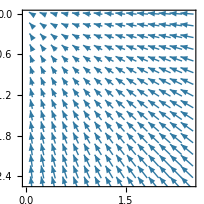
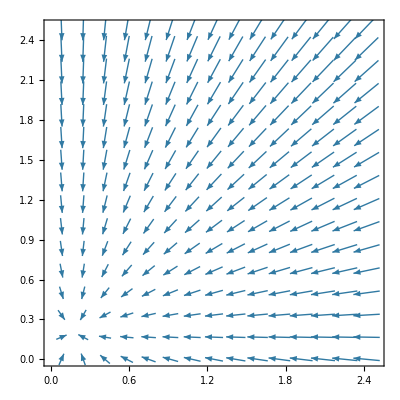

```mathematica
With[{t=1, s=0, r=0.7, p=0.2, epsilon=0.1, d=0.6, alpha=0.3},{VectorPlot[{ alpha (QvaluesGTvsGT[t, r, p, s, epsilon, d][[1]][[1]]-QvaluesGTvsGT[t, r, p, s, epsilon, d][[1]][[2]]-x), alpha (QvaluesADvsAD[t, r, p, s, epsilon, d][[1]][[1]]- QvaluesADvsAD[t, r, p, s, epsilon, d][[1]][[2]]-y)}, {x,0, 1/(1-d)}, {y,- 1/(1-d), 0}, Axes->True, VectorScale->{Medium,1/3,Automatic},VectorScaling->Automatic, VectorColorFunction->None]
,
VectorPlot[{ alpha (QvaluesGTvsGT[t, r, p, s, epsilon, d][[2]][[1]]-QvaluesGTvsGT[t, r, p, s, epsilon, d][[2]][[2]]-x), alpha (QvaluesADvsAD[t, r, p, s, epsilon, d][[2]][[1]]- QvaluesADvsAD[t, r, p, s, epsilon, d][[2]][[2]]-y)}, {x,0,1/(1-d)}, {y,0, 1/(1-d)}, Axes->True, VectorScale->{Medium,1/3,Automatic},VectorScaling->Automatic, VectorColorFunction->None]}]
```